```mathematica
(* MKM 505E - Advanced Control Methods in Mechatronics - Midterm Exam *)
```

```mathematica
(* Mertcan Kaya (518192004) *)
```

```mathematica
(* Question 2 *)
```

```mathematica
(* State-Space Description *)
```

```mathematica
Amat={{-0.02,0.005,2.4,-32},{-0.14,0.44,-1.3,-30},{0,0.018,-1.6,1.2},{0,0,1,0}};
```

```mathematica
Bmat={{0.14,-0.12},{0.36,-8.6},{0.35,0.009},{0,0}};
```

```mathematica
Cmat={{0,1,0,0},{0,0,0,57.3}};
```

```mathematica
Dmat={{0,0},{0,0}};
```

```mathematica
SSmat=ArrayFlatten[{{Amat,Bmat},{Cmat,Dmat}}];
```

```mathematica
MatrixForm[SSmat]
```

(-0.02 | 0.005 | 2.4 | -32 | 0.14 | -0.12
-0.14 | 0.44 | -1.3 | -30 | 0.36 | -8.6
0 | 0.018 | -1.6 | 1.2 | 0.35 | 0.009
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 57.3 | 0 | 0)

```mathematica
Eigenvalues[Amat]
```

{-2.22787+0. ⅈ,0.491325+0.415134 ⅈ,0.491325-0.415134 ⅈ,0.0652236+0. ⅈ}

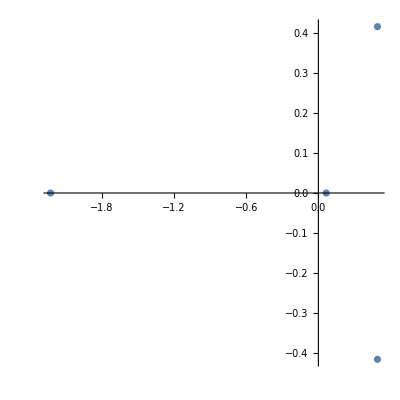

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{-2.227873174668408+0. ⅈ,0.4913248042452636+0.4151343894001922 ⅈ,0.4913248042452636-0.4151343894001922 ⅈ,0.06522356617788029+0. ⅈ},AspectRatio->1]
```

```mathematica
(* Estimate F and G matrices *)
```

```mathematica
Fmat={{-1,0,0,0},{0,-2,0,0},{0,0,-3,0},{0,0,0,-4}};
```

```mathematica
MatrixForm[Fmat]
```

(-1 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -3 | 0
0 | 0 | 0 | -4)

```mathematica
Gmat={{1,2},{2,3},{3,4},{4,5}};
```

```mathematica
MatrixForm[Gmat]
```

(1 | 2
2 | 3
3 | 4
4 | 5)

```mathematica
(* Check (A,C) is observable *)
```

```mathematica
ObsMat={{Cmat},{Cmat.Amat},{Cmat.MatrixPower[Amat,2]},{Cmat.MatrixPower[Amat,3]}};
```

```mathematica
MatrixRank[ArrayFlatten[ObsMat]]
```

4

```mathematica
(* rank(ObsMat)=4=n, (A,C) is observable *)
```

```mathematica
(* Check (F,G) is controllable *)
```

```mathematica
CtrMat={{Gmat,Fmat.Gmat,MatrixPower[Fmat,2].Gmat,MatrixPower[Fmat,3].Gmat}};
```

```mathematica
MatrixRank[ArrayFlatten[CtrMat]]
```

4

```mathematica
(* rank(CtrMat)=4=n, (F,G) is controllable *)
```

```mathematica
(* -FX+XA=GC, LyapunovSolve[-F,A,GC] *)
```

```mathematica
Xmat=LyapunovSolve[-Fmat,Amat,Gmat.Cmat];
```

```mathematica
MatrixForm[Xmat]
```

(-0.0117382 | -0.0821676 | 62.1322 | 37.2007
-0.10699 | -1.51315 | 316.256 | -128.213
0.0628085 | 1.33692 | -88.8519 | 125.98
0.0370216 | 1.05247 | -37.3978 | 91.034)

```mathematica
XmatInv=Inverse[Xmat];
```

```mathematica
MatrixForm[XmatInv]
```

(-37.8567 | 32.7562 | 153.738 | -151.151
-1.17795 | -0.116633 | -3.28679 | 4.86561
-0.00801532 | 0.0105963 | 0.0316064 | -0.02554
0.0257213 | -0.00761971 | -0.0115383 | 0.00570989)

```mathematica
(* Xmat is invertable (non-singular) *)
```

```mathematica
Pmat=Xmat.Bmat;
```

```mathematica
MatrixForm[Pmat]
```

(21.7151 | 1.26724
110.13 | 15.8722
-30.6081 | -12.3048
-12.7052 | -9.39228)